# Числено интегриране. Квадратурни формули на Нютон-Коутс

Задача: (a и b са съответно предпоследната и последната цифра от факултетния номер)
Дадена е функцията f(x) = (b + 2 - x)/(2 x^2+a+1)
1. Табулирайте функцията f(x) в интервала [a, a+b+1], като разделите интервала на b+5 равни части.
2. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на левите правоъгълници, използвайки точките получени в 1. Каква е грешката на полученото приближение?
3. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на десните правоъгълници, използвайки точките получени в 1. Каква е грешката на полученото приближение?
4. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на средните правоъгълници, използвайки точките получени в 1. Каква е грешката на полученото приближение?
5. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на трапеците, използвайки точките получени в 1. Каква е грешката на полученото приближение?
6. Може ли по построената в 1 таблица да се използва квадратурната формула на Симпсън за изчисляване на интеграла ∫_a^(a+b+1) f(x)ⅆx? Обосновете отговора си. Ако може, го изчислете и пресметнете каква е грешката на полученото приближение?
7. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на левите правоъгълници с точност 0.00001.
8. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на десните правоъгълници с точност 0.00001.
9. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на средните правоъгълници с точност 0.00001.
10. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на трапеците с точност 0.00001.
11. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на Симпсън с точност 0.00001.

## Съставяне на мрежата

```mathematica
f[x_]:=(11-x)/(2 x^2 + 2)
a = 1.; b = 11.;
h = (b-a)/n;
n = 14;
Print["Мрежата е с брой подинтервали n = ", n, " и стъпка h = ",h]
xt = Table[a + i*h, {i,0,n}]
```

Мрежата е с брой подинтервали n = 14 и стъпка h = 0.714286

{1.,1.71429,2.42857,3.14286,3.85714,4.57143,5.28571,6.,6.71429,7.42857,8.14286,8.85714,9.57143,10.2857,11.}

```mathematica
f[xt]
```

{2.5,1.17876,0.621302,0.361163,0.224936,0.146785,0.0987306,0.0675676,0.0465013,0.0317835,0.021225,0.0134857,0.00771265,0.00334416,7.28015×10^-18}

## Леви правоъгълници

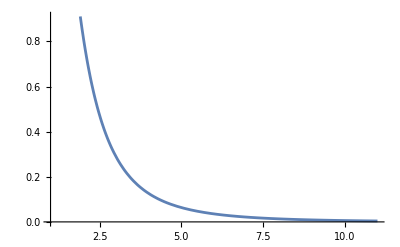

```mathematica
Plot[Abs[f'[x]],{x,a,b}]
```

```mathematica
a = 1.;b= 11.;
h = (b -a)/n;
n = 14;
f[x_]:= (11-x)/(2 x^2 + 2)
Itochno = ∫_a^b f[x]ⅆx ;
I1 = h*∑_(i=0)^(n-1) f[a+i*h];
M1 = Abs[f'[a]];
R1 = (b-a)^2/(2n)*M1;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на левите правоъгълници е ", I1]
Print["Точната стойност                                           е ", Itochno]
Print["Теоретичната грешка по формулата на левите правоъгълници   е ", R1]
Print["Истинската грешка по формулата на левите правоъгълници     е ", Abs[I1-Itochno]]
```

Мрежата е със стъпка 0.714286 и брой подинтервали 14

Приближената стойност по формулата на левите правоъгълници е 3.80235

Точната стойност                                           е 2.79334

Теоретичната грешка по формулата на левите правоъгълници   е 9.82143

Истинската грешка по формулата на левите правоъгълници     е 1.00901

## Десни правоъгълници

```mathematica
Plot[Abs[f'[x]],{x,a,b}]
```

-Graphics-

```mathematica
a = 1.;b= 11.;
h = (b -a)/n;
n = 14;
f[x_]:= (11-x)/(2 x^2 + 2)
Itochno = ∫_a^b f[x]ⅆx ;
I2 = h*∑_(i=0)^n f[a+i*h];
M2 = Abs[f'[a]];
R2 = (b-a)^2/(2n)*M2;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на левите правоъгълници е ", I2]
Print["Точната стойност                                           е ", Itochno]
Print["Теоретичната грешка по формулата на левите правоъгълници   е ", R2]
Print["Истинската грешка по формулата на левите правоъгълници     е ", Abs[I2-Itochno]]
```

Мрежата е със стъпка 0.714286 и брой подинтервали 14

Приближената стойност по формулата на левите правоъгълници е 3.80235

Точната стойност                                           е 2.79334

Теоретичната грешка по формулата на левите правоъгълници   е 9.82143

Истинската грешка по формулата на левите правоъгълници     е 1.00901

## Средни правоъгълници

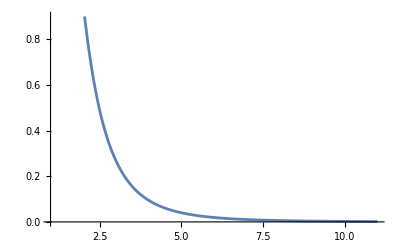

```mathematica
Plot[Abs[f''[x]],{x,a,b}]
```

```mathematica
a = 1.;b= 11.;
h = (b -a)/n;
n = 14;
f[x_]:= (11-x)/(2 x^2 + 2)
Itochno = ∫_a^b f[x]ⅆx ;
I3 = h*∑_(i=0)^(n-1) f[a+i*h + h/2];
M3 = Abs[f''[a]];
R3= (b-a)^3/(24 n^2)*M3;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на левите правоъгълници е ", I3]
Print["Точната стойност                                           е ", Itochno]
Print["Теоретичната грешка по формулата на левите правоъгълници   е ", R3]
Print["Истинската грешка по формулата на левите правоъгълници     е ", Abs[I3-Itochno]]
```

Мрежата е със стъпка 0.714286 и брой подинтервали 14

Приближената стойност по формулата на левите правоъгълници е 2.73552

Точната стойност                                           е 2.79334

Теоретичната грешка по формулата на левите правоъгълници   е 0.637755

Истинската грешка по формулата на левите правоъгълници     е 0.0578239

## Трапеци

```mathematica
Plot[Abs[f''[x]],{x,a,b}]
```

-Graphics-

```mathematica
a = 1.;b= 11.;
h = (b -a)/n;
n = 14;
f[x_]:= (11-x)/(2 x^2 + 2)
Itochno = ∫_a^b f[x]ⅆx ;
IT = h/2*(f[a]+2∑_(i=1)^(n-1) f[a+i*h]+f[b]);
M2 = Abs[f''[a]];
RT = (b-a)^3/(12 n^2)*M2;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на трапците е ", IT]
Print["Точната стойност                               е ", Itochno]
Print["Теоретичната грешка по формулата на трапците   е ", RT]
Print["Истинската грешка по формулата на трапците     е ", Abs[IT-Itochno]]
```

Мрежата е със стъпка 0.714286 и брой подинтервали 14

Приближената стойност по формулата на трапците е 2.90949

Точната стойност                               е 2.79334

Теоретичната грешка по формулата на трапците   е 1.27551

Истинската грешка по формулата на трапците     е 0.116153

## Симпсън

Може да използваме формулата на Симпсън, тъй като броят на подинтервалите е четно число - в случая 14.

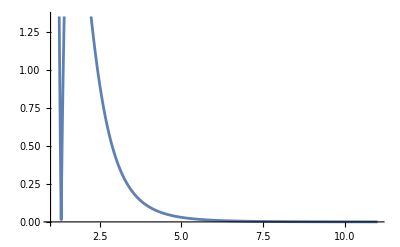

```mathematica
Plot[Abs[f''''[x]],{x,a,b}]
```

```mathematica
a = 1.;b= 11.;
h = (b -a)/n;
n = 14;
f[x_]:= (11-x)/(2 x^2 + 2)
Itochno = ∫_a^b f[x]ⅆx ;
m = n /2;
IS = h/3*(f[a]+4∑_(i=1)^m f[a+(2i-1)*h]+2∑_(i=1)^(m-1) f[a+(2i)*h]+f[b]);
M4 = Abs[f''''[a]];
RS = (b-a)^5/(180 n^4)*M4;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на Симпсън  е ", IS]
Print["Точната стойност                               е ", Itochno]
Print["Теоретичната грешка по формулата на Симпсън    е ", RS]
Print["Истинската грешка по формулата на Симпсън      е ", Abs[IS-Itochno]]
```

Мрежата е със стъпка 0.714286 и брой подинтервали 14

Приближената стойност по формулата на Симпсън  е 2.79818

Точната стойност                               е 2.79334

Теоретичната грешка по формулата на Симпсън    е 0.216924

Истинската грешка по формулата на Симпсън      е 0.00483789

# Пресмятане с предварително зададена точност

## Леви правоъгълници

```mathematica
eps = 10^-5;
Clear[n]
Reduce[(b-a)^2/(2n)*M1<=eps, n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n<0||n≥1.375×10^7

```mathematica
a = 1.;b= 11.;
h = (b -a)/n;
n = 1.375*10^7;
f[x_]:= (11-x)/(2 x^2 + 2)
Itochno = ∫_a^b f[x]ⅆx ;
I1 = h*∑_(i=0)^(n-1) f[a+i*h];
M1 = Abs[f'[a]];
R1 = (b-a)^2/(2n)*M1;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n] 
Print["Приближената стойност по формулата на левите правоъгълници е ", I1]
Print["Точната стойност                                           е ", Itochno]
Print["Теоретичната грешка по формулата на левите правоъгълници   е ", R1]
Print["Истинската грешка по формулата на левите правоъгълници     е ", Abs[I1-Itochno]]
```

Мрежата е със стъпка 7.27273×10^-7 и брой подинтервали 1.375×10^7

Приближената стойност по формулата на левите правоъгълници е 2.79334

Точната стойност                                           е 2.79334

Теоретичната грешка по формулата на левите правоъгълници   е 0.00001

Истинската грешка по формулата на левите правоъгълници     е 9.11591×10^-7

## Десни правоъгълници

```mathematica
eps = 10^-5;
Clear[n]
Reduce[(b-a)^2/(2n)*M2<=eps, n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n<0||n≥1.5×10^7

```mathematica
a = 1.;b= 11.;
h = (b -a)/n;
n= 1.5*10^7;
f[x_]:= (11-x)/(2 x^2 + 2)
Itochno = ∫_a^b f[x]ⅆx ;
I2 = h*∑_(i=0)^n f[a+i*h];
M2 = Abs[f'[a]];
R2 = (b-a)^2/(2n)*M2;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n] // N
Print["Приближената стойност по формулата на левите правоъгълници е ", I2]
Print["Точната стойност                                           е ", Itochno]
Print["Теоретичната грешка по формулата на левите правоъгълници   е ", R2]
Print["Истинската грешка по формулата на левите правоъгълници     е ", Abs[I2-Itochno]]
```

Мрежата е със стъпка 6.66667×10^-7 и брой подинтервали 1.5×10^7

Приближената стойност по формулата на левите правоъгълници е 2.79334

Точната стойност                                           е 2.79334

Теоретичната грешка по формулата на левите правоъгълници   е 9.16667×10^-6

Истинската грешка по формулата на левите правоъгълници     е 8.35833×10^-7

## Средни правоъгълници

```mathematica
eps = 10^-5;
Clear[n]
Reduce[(b-a)^3/(24 n^2)*M3<=eps, n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n≤-3535.53||n≥3535.53

```mathematica
a = 1.;b= 11.;

n = 3535.53;
h = (b -a)/n;
f[x_]:= (11-x)/(2 x^2 + 2)
Itochno = ∫_a^b f[x]ⅆx ;
I3 = h*∑_(i=0)^(n-1) f[a+i*h + h/2];
M3 = Abs[f''[a]];
R3= (b-a)^3/(24 n^2)*M3;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на левите правоъгълници е ", I3]
Print["Точната стойност                                           е ", Itochno]
Print["Теоретичната грешка по формулата на левите правоъгълници   е ", R3]
Print["Истинската грешка по формулата на левите правоъгълници     е ", Abs[I3-Itochno]]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n≤-3535.53||n≥3535.53

Мрежата е със стъпка 0.00282843 и брой подинтервали 3535.53

Приближената стойност по формулата на левите правоъгълници е 2.79334

Точната стойност                                           е 2.79334

Теоретичната грешка по формулата на левите правоъгълници   е 0.00001

Истинската грешка по формулата на левите правоъгълници     е 9.17408×10^-7

## Трапеци

```mathematica
eps = 10^-5;
Clear[n]
Reduce[(b-a)^3/(12 n^2)*M3<=eps, n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n≤-5000.||n≥5000.

```mathematica
a = 1.;b= 11.;

n = 5000;
h = (b -a)/n;
f[x_]:= (11-x)/(2 x^2 + 2)
Itochno = ∫_a^b f[x]ⅆx ;
IT = h/2*(f[a]+2∑_(i=1)^(n-1) f[a+i*h]+f[b]);
M2= Abs[f''[a]];
RT = (b-a)^3/(12 n^2)*M2;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на трапците е ", IT]
Print["Точната стойност                               е ", Itochno]
Print["Теоретичната грешка по формулата на трапците   е ", RT]
Print["Истинската грешка по формулата на трапците     е ", Abs[IT-Itochno]]
```

Мрежата е със стъпка 0.002 и брой подинтервали 5000

Приближената стойност по формулата на трапците е 2.79334

Точната стойност                               е 2.79334

Теоретичната грешка по формулата на трапците   е 0.00001

Истинската грешка по формулата на трапците     е 9.17801×10^-7

## Симпсън

```mathematica
eps = 10^-5;
Clear[n]
Reduce[(b-a)^5/(180 n^4)*M4<=eps, n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n≤-169.904||n≥169.904

```mathematica
a = 1.;b= 11.;
n = 169.904;
h = (b -a)/n;
f[x_]:= (11-x)/(2 x^2 + 2)
Itochno = ∫_a^b f[x]ⅆx ;
m = n /2;
IS = h/3*(f[a]+4∑_(i=1)^m f[a+(2i-1)*h]+2∑_(i=1)^(m-1) f[a+(2i)*h]+f[b]);
M4 = Abs[f''''[a]];
RS = (b-a)^5/(180 n^4)*M4;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на Симпсън  е ", IS]
Print["Точната стойност                               е ", Itochno]
Print["Теоретичната грешка по формулата на Симпсън    е ", RS]
Print["Истинската грешка по формулата на Симпсън      е ", Abs[IS-Itochno]]
```

Мрежата е със стъпка 0.0588568 и брой подинтервали 169.904

Приближената стойност по формулата на Симпсън  е 2.79331

Точната стойност                               е 2.79334

Теоретичната грешка по формулата на Симпсън    е 0.0000100001

Истинската грешка по формулата на Симпсън      е 0.0000352253